### 3D Pyrochlore Lattice

```mathematica
Table[0,{i,4},{j,4}]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
MatrixForm[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
```

```mathematica
Clear[c]
```

#### Define the hamiltonian of simple Pyrochlore Lattice (Coeffecient doesn’t matter)

```mathematica
H=-({{0, Cos[b], Cos[c], Cos[d]}, {Cos[b], 0, Cos[c-b], Cos[d-b]}, {Cos[c], Cos[c-b], 0, Cos[d-c]}, {Cos[d], Cos[d-b], Cos[d-c], 0}});
```

```mathematica
Eigenvalues[H]
```

{1,1,1/2 (-2-√2 √(2+Cos[2 b]+Cos[2 b-2 c]+Cos[2 c]+Cos[2 b-2 d]+Cos[2 c-2 d]+Cos[2 d])),1/2 (-2+√2 √(2+Cos[2 b]+Cos[2 b-2 c]+Cos[2 c]+Cos[2 b-2 d]+Cos[2 c-2 d]+Cos[2 d]))}

```mathematica
Define the dispersion Function
F[b_,c_,d_]:={1,1,1/2 (-2-√2 √(2+Cos[2 b]+Cos[2 b-2 c]+Cos[2 c]+Cos[2 b-2 d]+Cos[2 c-2 d]+Cos[2 d])),1/2 (-2+√2 √(2+Cos[2 b]+Cos[2 b-2 c]+Cos[2 c]+Cos[2 b-2 d]+Cos[2 c-2 d]+Cos[2 d]))}
```

#### Plot the dispersion Function Along High Symmetry Points Loop

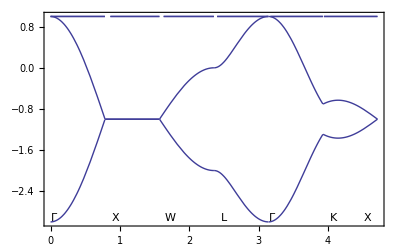

```mathematica
Plot[Piecewise[{{F[2t,0,2t],t≥0&&t<Pi/4},{F[Pi/2,t-Pi/4,t-Pi/4+Pi/2],t≥Pi/4&&t<Pi/2},{F[Pi/2,Pi/4+t-Pi/2,3Pi/4-t+Pi/2],t≥Pi/2&&t<3Pi/4},{F[Pi/2-2(t-3Pi/4),Pi/2-2(t-3Pi/4),Pi/2-2(t-3Pi/4)],t≥3Pi/4&&t<Pi},{F[3/2(t-Pi),3/2(t-Pi),3(t-Pi)],t≥Pi&&t<5Pi/4},{F[3Pi/8+t/2-5Pi/8,3Pi/8-3t/2+15Pi/8,3Pi/4-(t-5Pi/4)],t≥5Pi/4&&t≤3Pi/2}}],{t,0,3Pi/2},GridLines->{{{Pi/4,Dashed},{2Pi/4,Dashed},{3Pi/4,Dashed},{Pi,Dashed},{5Pi/4,Dashed},{3Pi/2,Dashed}},{}},Epilog->{Inset["Γ",{0.05,0.08-3}],Inset["X",{Pi/4+0.15,0.08-3}],Inset["W",{2Pi/4+0.15,0.08-3}],Inset["L",{3Pi/4+0.15,0.08-3}],Inset["Γ",{Pi+0.05,0.08-3}],Inset["K",{5Pi/4+0.15,0.08-3}],Inset["X",{6Pi/4-0.15,0.08-3}]},Frame->True]
```